```mathematica
gf[ω_, Temp_]:= 1/(Exp[ω/Temp]+ 1);gb[ω_, Temp_]:= 1/(Exp[ω/Temp]- 1);
```

```mathematica
me = 0 5.11 10^-4;
mchi = 100; 
Γ = 10^-5;
δm = 10^-1;
msel = mchi + δm;
MP = 2.4 10^18;  

cons = 10^-17.;
```

```mathematica
MsToy[s_]:=cons mchi^4/((s -msel^2)^2 + msel^2 Γ^2)
```

#### Kinematics

```mathematica
m1 = me;  m2= mchi; m3 = me; m4  = mchi;

E1cm = (s + m1^2 - m2^2)/(2  Sqrt[s]); E2cm = (s + m2^2- m1^2)/(2 Sqrt[s]);  E3cm = (s + m3^2- m4^2)/(2 Sqrt[s]);  E4cm = (s + m4^2- m3^2)/(2 Sqrt[s]); 
p1cm = Sqrt[E1cm^2 - m1^2]; p2cm = Sqrt[E2cm^2 - m2^2]; p3cm = Sqrt[E3cm^2 - m3^2]; p4cm = Sqrt[E4cm^2 - m4^2];
```

```mathematica
t0 =(E1cm - E3cm)^2 - (p1cm - p3cm)^2//FullSimplify;
```

```mathematica
t1 = FullSimplify[(E1cm - E3cm)^2 - (p1cm - p3cm)^2- 4 p1cm p3cm ];
```

```mathematica
σt[ss_]:= Integrate[-t MsToy[ss], {t, t1, t0}]/.{s-> ss};
```

```mathematica
Tmin = 10^-4; T0=100;
```

```mathematica
aToy[Temp_?NumericQ]:= (5/(2 (2 π)^9))^(1/2)MP/mchi^3 1/Temp^2 NIntegrate[ gf[ω, Temp]D[ω^4 σt[ mchi^2 + mchi ω], ω] ,{ω,0,Infinity}]
```

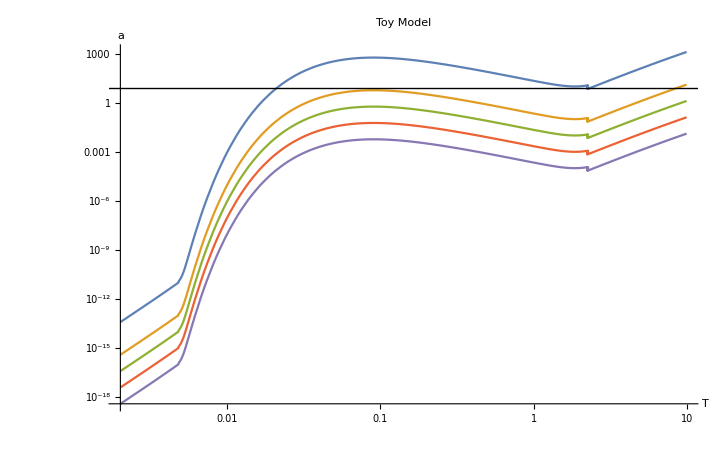

```mathematica
aPlot = LogLogPlot[{10 aToy[Temp], 0.1aToy[Temp], 0.01aToy[Temp],10^-3 aToy[Temp], 10^-4 aToy[Temp]}, {Temp,20Tmin,0.1 T0}, GridLines->Automatic,AxesLabel->{HoldForm[T],HoldForm[a]},PlotLabel->HoldForm[Toy Model],LabelStyle->{GrayLevel[0]}, Epilog->{Line[{{-10,2},{T0, 2}}] }]
```

Having Γ < 10^-8 gives non-sensical results for T ∈~(0.003, 0.02)

```mathematica
DEQTOY2= {Tchi'[Temp] - (2 + 10 aToy[ Temp]) Tchi[Temp]/Temp==-10 aToy[ Temp],Tchi[T0]==T0};DEQTOY3=  {Tchi'[Temp] - (2 + 0.1 aToy[ Temp]) Tchi[Temp]/Temp==- 0.1aToy[ Temp],Tchi[T0]==T0};DEQTOY4=  {Tchi'[Temp] - (2 + 0.01aToy[ Temp]) Tchi[Temp]/Temp==- 0.01aToy[ Temp],Tchi[T0]==T0};DEQTOY5=  {Tchi'[Temp] - (2 + 10^-3 aToy[ Temp]) Tchi[Temp]/Temp==- 10^-3 aToy[ Temp],Tchi[T0]==T0};DEQTOY6=  {Tchi'[Temp] - (2 + 10^-4 aToy[ Temp]) Tchi[Temp]/Temp==- 10^-4 aToy[ Temp],Tchi[T0]==T0};

TempToy2 = NDSolve[DEQTOY2, Tchi, {Temp,Tmin,T0}];
TempToy3 = NDSolve[DEQTOY3, Tchi, {Temp,Tmin,T0}];
TempToy4 = NDSolve[DEQTOY4, Tchi, {Temp,Tmin,T0}];
TempToy5 = NDSolve[DEQTOY5, Tchi, {Temp,Tmin,T0}];
TempToy6 = NDSolve[DEQTOY6, Tchi, {Temp,Tmin,T0}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.000649646}. NIntegrate obtained 5.06145×10^-40 and 7.36247×10^-46 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.199086}. NIntegrate obtained 5.58864×10^-9 and 2.34703×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.000649646}. NIntegrate obtained 5.06145×10^-40 and 7.36247×10^-46 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.199086}. NIntegrate obtained 6.03226×10^-9 and 2.34948×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.000649646}. NIntegrate obtained 5.06145×10^-40 and 7.36247×10^-46 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.199086}. NIntegrate obtained 4.83875×10^-9 and 2.34185×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.000649646}. NIntegrate obtained 5.06145×10^-40 and 7.36247×10^-46 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.199086}. NIntegrate obtained 4.60122×10^-9 and 2.33983×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.000649646}. NIntegrate obtained 5.06145×10^-40 and 7.36247×10^-46 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {0.199086}. NIntegrate obtained 4.46312×10^-9 and 2.33853×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
TrecPlot = LogLogPlot[{Evaluate[Tchi[x]/x/.TempToy2],Evaluate[Tchi[x]/x/.TempToy3],Evaluate[Tchi[x]/x/.TempToy4],Evaluate[Tchi[x]/x/.TempToy5],Evaluate[Tchi[x]/x/.TempToy6]}, {x,100  Tmin/mchi, 100 T0/mchi}];
```

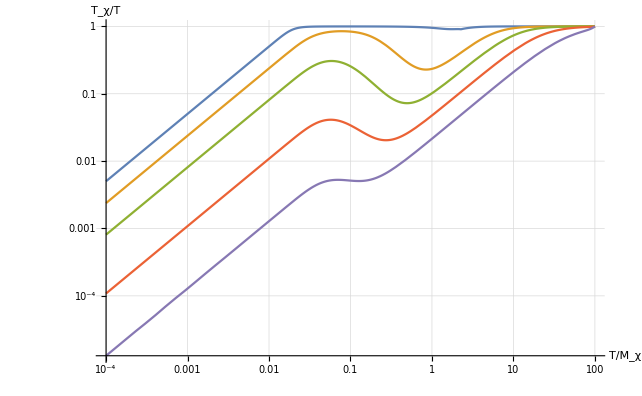

```mathematica
Show[TrecPlot,AxesLabel->{HoldForm[T/Subscript[M, χ]],HoldForm[Subscript[T, χ]/T]},GridLines->Automatic,PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```